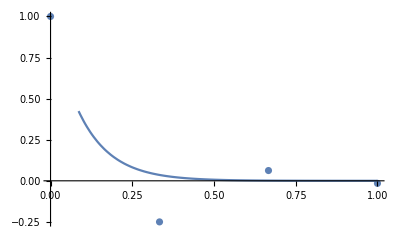
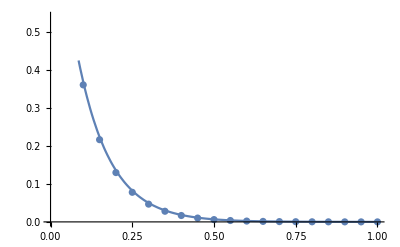
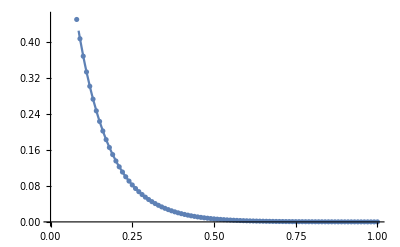

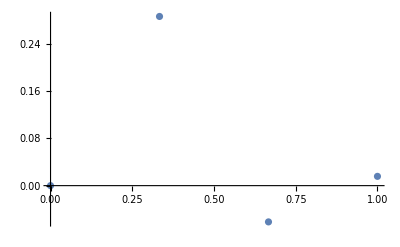
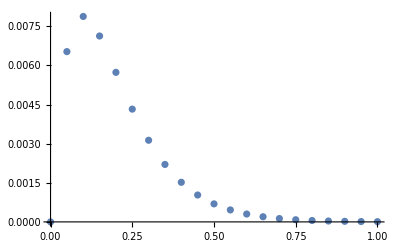
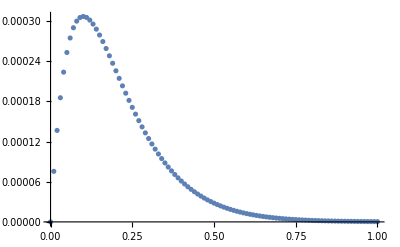

```mathematica
NewtonSolve[f_, x0_, nmax_]:=Module[
{xprev, xcurr, i},
xprev = x0;

For[i=1, i≤nmax, i++,
xcurr = xprev-(f/.x->xprev)/(D[f, x]/.x->xprev);
If[Abs[xcurr-xprev]<10^6, 
Return[xcurr]];
xprev=xcurr;
];
xcurr
]
EulerForward[du_, du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret},

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];

y[[1]] = du0;

For[i = 2, i≤ Length[t], i++,
y[[i]] = y[[i-1]]+h(du[t0+(i-1)*h,y[[i-1]]]);
];

ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]//N
]
EulerBetter[du_,du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret, aprY},

aprY = EulerForward[du,du0, t0, T, n];

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];
y[[1]] = du0;

For[i = 1, i≤ Length[t]-1, i++,
y[[i+1]]= NewtonSolve[y[[i]]+h/2*du[0,x]+h/2*du[0,y[[i]]]-x, aprY[[i+1,2]],10];

];
ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]
]

f[t_, u_]:=Module[
{},
-10u
]
exactSol[t_]=u[t]/.DSolve[{u'[t]==-10 u[t],u[0]==1},u[t],t][[1]];
n={3,20,100};
Table[Show[
ListPlot[EulerBetter[f, 1,0,1,n[[i]]]],
Plot[exactSol[t], {t,0,1}
]
], {i, 1,3,1}]
aproxSolutionsOF =Table[EulerBetter[f, 1,0,1,n[[i]]], {i, 1,3,1}];
hres = {};
res={};
For[i=1,i<=Length[aproxSolutionsOF],i++,
For[j=1, j<=Length[aproxSolutionsOF[[i]]],j++,
AppendTo[hres, {aproxSolutionsOF[[i,j,1]],-aproxSolutionsOF[[i,j,2]]+exactSol[aproxSolutionsOF[[i,j,1]]]}]
];
AppendTo[res,hres];
hres = {};
]
Table[ListPlot[res[[i]]],{i,1,3, 1}]
Animate[
Show[
ListPlot[EulerBetter[f, 1,0,1,i],PlotRange->2],
Plot[exactSol[t], {t,0,1}]
],{i,4,100,1},
AnimationRate->1,
AnimationRunning->False
]
```

```mathematica
exactSol2[t_]=u[t]/.DSolve[{u'[t]==10 u[t](1-u[t]),u[0]==0.1},u[t],t][[1]];
f2[t_,u_]:=10u(1-u);
n2= {10,20,35,75,500};
EulerBackwardsV2[du_,du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret, aprY},

aprY = EulerForward[du,du0, t0, T, n];

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];
y[[1]] = du0;

For[i = 1, i≤ Length[t]-1, i++,
y[[i+1]]= NewtonSolve[y[[i]]+h*du[0,x]-x, aprY[[i+1,2]],10];

];
ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

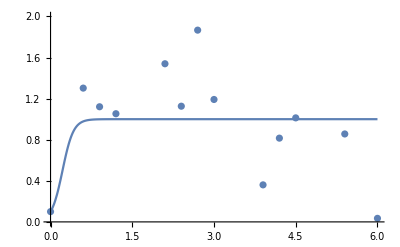
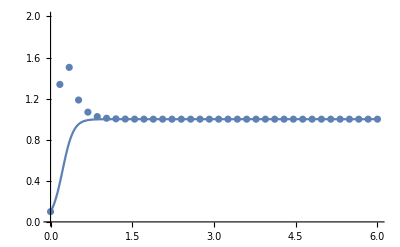
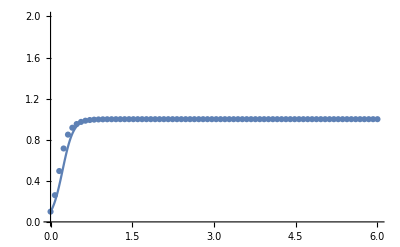
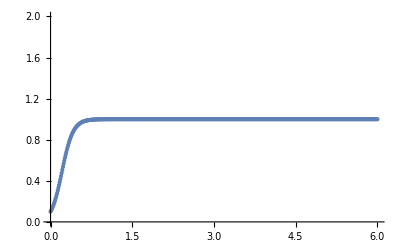
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[
ListPlot[EulerBackwardsV2[f2, 0.1,0,6,n2[[i]]],PlotRange->2],
Plot[exactSol2[t], {t,0,6},PlotRange->2
]
], {i, 1,5,1}]
```